# Ejemplo 2 Manivela - Corredera

## Funciones

```mathematica
(*Matrices de Rotación*)
Rx[γ_]:=({{1, 0, 0}, {0, Cos[γ], -Sin[γ]}, {0, Sin[γ], Cos[γ]}});
Ry[β_]:=({{Cos[β], 0, Sin[β]}, {0, 1, 0}, {-Sin[β], 0, Cos[β]}});
Rz[α_]:=({{Cos[α], -Sin[α], 0}, {Sin[α], Cos[α], 0}, {0, 0, 1}});

MatrixForm[Rx[A]]
MatrixForm[Ry[A]]
MatrixForm[Rz[A]]
```

(1 | 0 | 0
0 | Cos[A] | -Sin[A]
0 | Sin[A] | Cos[A])

(Cos[A] | 0 | Sin[A]
0 | 1 | 0
-Sin[A] | 0 | Cos[A])

(Cos[A] | -Sin[A] | 0
Sin[A] | Cos[A] | 0
0 | 0 | 1)

## Datos

```mathematica
z10=0.03;(*m*)
x32=0.08;
z43=0.015;
z87=0.3;
y1211=0.1;
z1312=0.12;
β1413=90*Degree;
β1514=270*Degree;
```

## Ecuaciones Cinemáticas

```mathematica
Clear[θ21, θ54, θ65, θ76, θ98,θ109,x1110];
Clear[dθ21, dθ54, dθ65, dθ76, dθ98,dθ109,dx1110];
Clear[ddθ21, ddθ54, ddθ65, ddθ76, ddθ98,ddθ109,ddx1110];

(*-----------------------------Posicion-----------------------------*)
I3X3=IdentityMatrix[3];

C02=Rz[θ21];
C03=Rz[θ21];
C07=Rz[θ21].Rx[θ54].Ry[θ65].Rz[θ76];
C010=C07.Ry[θ98].Rx[θ109];
C011=C010;
C012=C010;

in={1,0,0};
jn={0,1,0};
kn={0,0,1};

i2=i10=in;
j11=jn;
k3=k7=k12=kn;

K0={0,0,1};
I2=C02.i2;
K3=C03.k3;
K7=C07.k7;
I10=C010.i10;
J11=C011.j11;
K12=C012.k12;


P10=z10*K0;
P32=x32*I2;
P43=z43*K3;

P87=z87*K7;
P1110=x1110*I10;
P1211=-y1211*J11;
P1312=z1312*K12;

(*-----------------------------Velocidad-----------------------------*)
C04=Rz[θ21];
C05=Rz[θ21].Rx[θ54];
C06=Rz[θ21].Rx[θ54].Ry[θ65];
C08=Rz[θ21].Rx[θ54].Ry[θ65].Rz[θ76];
C09=Rz[θ21].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ98];

i4=i9=in;
j5=j8=jn;
k6=kn;

K1=K0;
I4=C04.i4;
J5=C05.j5;
K6=C06.k6;
J8=C08.j8;
I9=C09.i9;

ω21=dθ21*K1;
ω54=dθ54*I4;
ω65=dθ65*J5;
ω76=dθ76*K6;
ω98=dθ98*J8;
ω109=dθ109*I9;

ω2=ω21;
ω7=ω21+ω54+ω65+ω76;

V10={0,0,0}; (*Asi definimos un vector 0*)
V32=ω2×P32;
V43={0,0,0};
V87=ω7×P87;
V1110=dx1110*I10;
V1211={0,0,0};
V1312={0,0,0};

(*-----------------------------Aceleracion-----------------------------*)
α21=ddθ21*K1;
α54=ddθ54*I4+ω21×ω54;
α65=ddθ65*J5+(ω21+ω54)×ω65;
α76=ddθ76*K6+(ω21+ω54+ω65)×ω76;
α98=ddθ98*J8+(ω21+ω54+ω65+ω76)×ω98;
α109=ddθ109*I9+(ω21+ω54+ω65+ω76+ω98)×ω109;

α2=α21;
α7=α21+α54+α65+α76;

A10={0,0,0}; 
A32=α2×P32+ω2×(ω2×P32);
A43={0,0,0};
A87=α7×P87+ω7×(ω7×P87);
A1110=ddx1110*I10;
A1211={0,0,0};
A1312={0,0,0};



Pos1=P10+P32+P43+P87+P1110+P1211+P1312;
Pos2=Rz[θ21].Rx[θ54].Ry[θ65].Rz[θ76].Ry[θ98].Rx[θ109].Rx[β1413].Ry[β1514]-I3X3;

(*FO = Funcion objetivo*)

FO = ∑_(i=1)^3 Pos1[[i]]^2+∑_(j=1)^3 ∑_(k=1)^3 Pos2[[j,k]]^2;


Vel1=V10+V32+V43+V87+V1110+V1211+V1312;
Vel2=ω21+ω54+ω65+ω76+ω98+ω109;

Acel1=A10+A32+A43+A87+A1110+A1211+A1312;
Acel2=α21+α54+α65+α76+α98+α109;


MatrixForm[Pos1]
MatrixForm[Pos2]
MatrixForm[Vel1]
MatrixForm[Acel1]
```

(0.+0.08 Cos[θ21]+0.3 (Cos[θ65] Sin[θ21] Sin[θ54]+Cos[θ21] Sin[θ65])+x1110 (Cos[θ98] (Cos[θ76] (Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65])-Cos[θ54] Sin[θ21] Sin[θ76])-(Cos[θ65] Sin[θ21] Sin[θ54]+Cos[θ21] Sin[θ65]) Sin[θ98])+0.12 (-Sin[θ109] (-Cos[θ54] Cos[θ76] Sin[θ21]-(Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65]) Sin[θ76])+Cos[θ109] (Cos[θ98] (Cos[θ65] Sin[θ21] Sin[θ54]+Cos[θ21] Sin[θ65])+(Cos[θ76] (Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65])-Cos[θ54] Sin[θ21] Sin[θ76]) Sin[θ98]))-0.1 (Cos[θ109] (-Cos[θ54] Cos[θ76] Sin[θ21]-(Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65]) Sin[θ76])+Sin[θ109] (Cos[θ98] (Cos[θ65] Sin[θ21] Sin[θ54]+Cos[θ21] Sin[θ65])+(Cos[θ76] (Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65])-Cos[θ54] Sin[θ21] Sin[θ76]) Sin[θ98]))
0.+0.08 Sin[θ21]+0.3 (-Cos[θ21] Cos[θ65] Sin[θ54]+Sin[θ21] Sin[θ65])+x1110 (Cos[θ98] (Cos[θ76] (Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65])+Cos[θ21] Cos[θ54] Sin[θ76])-(-Cos[θ21] Cos[θ65] Sin[θ54]+Sin[θ21] Sin[θ65]) Sin[θ98])+0.12 (-Sin[θ109] (Cos[θ21] Cos[θ54] Cos[θ76]-(Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65]) Sin[θ76])+Cos[θ109] (Cos[θ98] (-Cos[θ21] Cos[θ65] Sin[θ54]+Sin[θ21] Sin[θ65])+(Cos[θ76] (Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65])+Cos[θ21] Cos[θ54] Sin[θ76]) Sin[θ98]))-0.1 (Cos[θ109] (Cos[θ21] Cos[θ54] Cos[θ76]-(Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65]) Sin[θ76])+Sin[θ109] (Cos[θ98] (-Cos[θ21] Cos[θ65] Sin[θ54]+Sin[θ21] Sin[θ65])+(Cos[θ76] (Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65])+Cos[θ21] Cos[θ54] Sin[θ76]) Sin[θ98]))
0.045+0.3 Cos[θ54] Cos[θ65]+x1110 (Cos[θ98] (-Cos[θ54] Cos[θ76] Sin[θ65]+Sin[θ54] Sin[θ76])-Cos[θ54] Cos[θ65] Sin[θ98])+0.12 (-Sin[θ109] (Cos[θ76] Sin[θ54]+Cos[θ54] Sin[θ65] Sin[θ76])+Cos[θ109] (Cos[θ54] Cos[θ65] Cos[θ98]+(-Cos[θ54] Cos[θ76] Sin[θ65]+Sin[θ54] Sin[θ76]) Sin[θ98]))-0.1 (Cos[θ109] (Cos[θ76] Sin[θ54]+Cos[θ54] Sin[θ65] Sin[θ76])+Sin[θ109] (Cos[θ54] Cos[θ65] Cos[θ98]+(-Cos[θ54] Cos[θ76] Sin[θ65]+Sin[θ54] Sin[θ76]) Sin[θ98])))

(-1-Cos[θ109] (-Cos[θ54] Cos[θ76] Sin[θ21]-(Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65]) Sin[θ76])-Sin[θ109] (Cos[θ98] (Cos[θ65] Sin[θ21] Sin[θ54]+Cos[θ21] Sin[θ65])+(Cos[θ76] (Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65])-Cos[θ54] Sin[θ21] Sin[θ76]) Sin[θ98]) | -Sin[θ109] (-Cos[θ54] Cos[θ76] Sin[θ21]-(Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65]) Sin[θ76])+Cos[θ109] (Cos[θ98] (Cos[θ65] Sin[θ21] Sin[θ54]+Cos[θ21] Sin[θ65])+(Cos[θ76] (Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65])-Cos[θ54] Sin[θ21] Sin[θ76]) Sin[θ98]) | -Cos[θ98] (Cos[θ76] (Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65])-Cos[θ54] Sin[θ21] Sin[θ76])+(Cos[θ65] Sin[θ21] Sin[θ54]+Cos[θ21] Sin[θ65]) Sin[θ98]
-Cos[θ109] (Cos[θ21] Cos[θ54] Cos[θ76]-(Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65]) Sin[θ76])-Sin[θ109] (Cos[θ98] (-Cos[θ21] Cos[θ65] Sin[θ54]+Sin[θ21] Sin[θ65])+(Cos[θ76] (Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65])+Cos[θ21] Cos[θ54] Sin[θ76]) Sin[θ98]) | -1-Sin[θ109] (Cos[θ21] Cos[θ54] Cos[θ76]-(Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65]) Sin[θ76])+Cos[θ109] (Cos[θ98] (-Cos[θ21] Cos[θ65] Sin[θ54]+Sin[θ21] Sin[θ65])+(Cos[θ76] (Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65])+Cos[θ21] Cos[θ54] Sin[θ76]) Sin[θ98]) | -Cos[θ98] (Cos[θ76] (Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65])+Cos[θ21] Cos[θ54] Sin[θ76])+(-Cos[θ21] Cos[θ65] Sin[θ54]+Sin[θ21] Sin[θ65]) Sin[θ98]
-Cos[θ109] (Cos[θ76] Sin[θ54]+Cos[θ54] Sin[θ65] Sin[θ76])-Sin[θ109] (Cos[θ54] Cos[θ65] Cos[θ98]+(-Cos[θ54] Cos[θ76] Sin[θ65]+Sin[θ54] Sin[θ76]) Sin[θ98]) | -Sin[θ109] (Cos[θ76] Sin[θ54]+Cos[θ54] Sin[θ65] Sin[θ76])+Cos[θ109] (Cos[θ54] Cos[θ65] Cos[θ98]+(-Cos[θ54] Cos[θ76] Sin[θ65]+Sin[θ54] Sin[θ76]) Sin[θ98]) | -1-Cos[θ98] (-Cos[θ54] Cos[θ76] Sin[θ65]+Sin[θ54] Sin[θ76])+Cos[θ54] Cos[θ65] Sin[θ98])

(0.+0.3 dθ65 Cos[θ21] Cos[θ54]^2 Cos[θ65]-0.08 dθ21 Sin[θ21]+0.3 dθ54 Cos[θ54] Cos[θ65] Sin[θ21]+0.3 dθ21 Cos[θ21] Cos[θ65] Sin[θ54]+0.3 dθ65 Cos[θ21] Cos[θ65] Sin[θ54]^2-0.3 dθ21 Sin[θ21] Sin[θ65]-0.3 dθ65 Sin[θ21] Sin[θ54] Sin[θ65]+dx1110 (Cos[θ98] (Cos[θ76] (Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65])-Cos[θ54] Sin[θ21] Sin[θ76])-(Cos[θ65] Sin[θ21] Sin[θ54]+Cos[θ21] Sin[θ65]) Sin[θ98])
0.+0.08 dθ21 Cos[θ21]-0.3 dθ54 Cos[θ21] Cos[θ54] Cos[θ65]+0.3 dθ65 Cos[θ54]^2 Cos[θ65] Sin[θ21]+0.3 dθ21 Cos[θ65] Sin[θ21] Sin[θ54]+0.3 dθ65 Cos[θ65] Sin[θ21] Sin[θ54]^2+0.3 dθ21 Cos[θ21] Sin[θ65]+0.3 dθ65 Cos[θ21] Sin[θ54] Sin[θ65]+dx1110 (Cos[θ98] (Cos[θ76] (Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65])+Cos[θ21] Cos[θ54] Sin[θ76])-(-Cos[θ21] Cos[θ65] Sin[θ54]+Sin[θ21] Sin[θ65]) Sin[θ98])
0.-0.3 dθ54 Cos[θ21]^2 Cos[θ65] Sin[θ54]-0.3 dθ54 Cos[θ65] Sin[θ21]^2 Sin[θ54]-0.3 dθ65 Cos[θ21]^2 Cos[θ54] Sin[θ65]-0.3 dθ65 Cos[θ54] Sin[θ21]^2 Sin[θ65]+dx1110 (Cos[θ98] (-Cos[θ54] Cos[θ76] Sin[θ65]+Sin[θ54] Sin[θ76])-Cos[θ54] Cos[θ65] Sin[θ98]))

(0.-0.08 dθ21^2 Cos[θ21]+0.6 dθ21 dθ54 Cos[θ21] Cos[θ54] Cos[θ65]+0.3 ddθ65 Cos[θ21] Cos[θ54]^2 Cos[θ65]-0.08 ddθ21 Sin[θ21]+0.3 ddθ54 Cos[θ54] Cos[θ65] Sin[θ21]-0.6 dθ21 dθ65 Cos[θ54]^2 Cos[θ65] Sin[θ21]+0.3 ddθ21 Cos[θ21] Cos[θ65] Sin[θ54]-0.3 dθ21^2 Cos[θ65] Sin[θ21] Sin[θ54]-0.3 dθ54^2 Cos[θ21]^2 Cos[θ65] Sin[θ21] Sin[θ54]-0.3 dθ65^2 Cos[θ54]^2 Cos[θ65] Sin[θ21] Sin[θ54]-0.3 dθ54^2 Cos[θ65] Sin[θ21]^3 Sin[θ54]+0.3 ddθ65 Cos[θ21] Cos[θ65] Sin[θ54]^2-0.6 dθ21 dθ65 Cos[θ65] Sin[θ21] Sin[θ54]^2-0.3 dθ65^2 Cos[θ65] Sin[θ21] Sin[θ54]^3-0.3 dθ21^2 Cos[θ21] Sin[θ65]-0.3 dθ65^2 Cos[θ21]^3 Cos[θ54]^2 Sin[θ65]-0.3 ddθ21 Sin[θ21] Sin[θ65]-0.6 dθ54 dθ65 Cos[θ21]^2 Cos[θ54] Sin[θ21] Sin[θ65]-0.3 dθ65^2 Cos[θ21] Cos[θ54]^2 Sin[θ21]^2 Sin[θ65]-0.6 dθ54 dθ65 Cos[θ54] Sin[θ21]^3 Sin[θ65]-0.6 dθ21 dθ65 Cos[θ21] Sin[θ54] Sin[θ65]-0.3 ddθ65 Sin[θ21] Sin[θ54] Sin[θ65]-0.3 dθ65^2 Cos[θ21] Sin[θ54]^2 Sin[θ65]+ddx1110 (Cos[θ98] (Cos[θ76] (Cos[θ21] Cos[θ65]-Sin[θ21] Sin[θ54] Sin[θ65])-Cos[θ54] Sin[θ21] Sin[θ76])-(Cos[θ65] Sin[θ21] Sin[θ54]+Cos[θ21] Sin[θ65]) Sin[θ98])
0.+0.08 ddθ21 Cos[θ21]-0.3 ddθ54 Cos[θ21] Cos[θ54] Cos[θ65]+0.6 dθ21 dθ65 Cos[θ21] Cos[θ54]^2 Cos[θ65]-0.08 dθ21^2 Sin[θ21]+0.6 dθ21 dθ54 Cos[θ54] Cos[θ65] Sin[θ21]+0.3 ddθ65 Cos[θ54]^2 Cos[θ65] Sin[θ21]+0.3 dθ21^2 Cos[θ21] Cos[θ65] Sin[θ54]+0.3 dθ54^2 Cos[θ21]^3 Cos[θ65] Sin[θ54]+0.3 dθ65^2 Cos[θ21] Cos[θ54]^2 Cos[θ65] Sin[θ54]+0.3 ddθ21 Cos[θ65] Sin[θ21] Sin[θ54]+0.3 dθ54^2 Cos[θ21] Cos[θ65] Sin[θ21]^2 Sin[θ54]+0.6 dθ21 dθ65 Cos[θ21] Cos[θ65] Sin[θ54]^2+0.3 ddθ65 Cos[θ65] Sin[θ21] Sin[θ54]^2+0.3 dθ65^2 Cos[θ21] Cos[θ65] Sin[θ54]^3+0.3 ddθ21 Cos[θ21] Sin[θ65]+0.6 dθ54 dθ65 Cos[θ21]^3 Cos[θ54] Sin[θ65]-0.3 dθ21^2 Sin[θ21] Sin[θ65]-0.3 dθ65^2 Cos[θ21]^2 Cos[θ54]^2 Sin[θ21] Sin[θ65]+0.6 dθ54 dθ65 Cos[θ21] Cos[θ54] Sin[θ21]^2 Sin[θ65]-0.3 dθ65^2 Cos[θ54]^2 Sin[θ21]^3 Sin[θ65]+0.3 ddθ65 Cos[θ21] Sin[θ54] Sin[θ65]-0.6 dθ21 dθ65 Sin[θ21] Sin[θ54] Sin[θ65]-0.3 dθ65^2 Sin[θ21] Sin[θ54]^2 Sin[θ65]+ddx1110 (Cos[θ98] (Cos[θ76] (Cos[θ65] Sin[θ21]+Cos[θ21] Sin[θ54] Sin[θ65])+Cos[θ21] Cos[θ54] Sin[θ76])-(-Cos[θ21] Cos[θ65] Sin[θ54]+Sin[θ21] Sin[θ65]) Sin[θ98])
0.-0.3 dθ54^2 Cos[θ21]^2 Cos[θ54] Cos[θ65]-0.3 dθ65^2 Cos[θ21]^2 Cos[θ54]^3 Cos[θ65]-0.3 dθ54^2 Cos[θ54] Cos[θ65] Sin[θ21]^2-0.3 dθ65^2 Cos[θ54]^3 Cos[θ65] Sin[θ21]^2-0.3 ddθ54 Cos[θ21]^2 Cos[θ65] Sin[θ54]-0.3 ddθ54 Cos[θ65] Sin[θ21]^2 Sin[θ54]-0.3 dθ65^2 Cos[θ21]^2 Cos[θ54] Cos[θ65] Sin[θ54]^2-0.3 dθ65^2 Cos[θ54] Cos[θ65] Sin[θ21]^2 Sin[θ54]^2-0.3 ddθ65 Cos[θ21]^2 Cos[θ54] Sin[θ65]-0.3 ddθ65 Cos[θ54] Sin[θ21]^2 Sin[θ65]+0.6 dθ54 dθ65 Cos[θ21]^2 Sin[θ54] Sin[θ65]+0.6 dθ54 dθ65 Sin[θ21]^2 Sin[θ54] Sin[θ65]+ddx1110 (Cos[θ98] (-Cos[θ54] Cos[θ76] Sin[θ65]+Sin[θ54] Sin[θ76])-Cos[θ54] Cos[θ65] Sin[θ98]))

## Solución de la Posición

El análisis de posición falla por :
1. Un mal dato
2. Un mal vector
3. Una mala ecuación
4. Un mal valor inicial 
5. Error de sintaxis

### Solución inicial

```mathematica
Clear[θ21, θ54, θ65, θ76, θ98,θ109,x1110];
Clear[dθ21, dθ54, dθ65, dθ76, dθ98,dθ109,dx1110];
Clear[ddθ21, ddθ54, ddθ65, ddθ76, ddθ98,ddθ109,ddx1110];
θ21=0*Degree;
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
PosInicial=FindMinimum[FO,
{
{θ54,30*Degree},
{θ65,300*Degree},
{θ76,43*Degree},
{θ98,160*Degree},
{θ109,330*Degree},
{x1110,0.26}
}, MaxIterations ->15];
(*FindMinimum entrega un valor residual*)

{θ54, θ65, θ76, θ98,θ109}/Degree/.PosInicial[[2]]
PosInicial
```

{30.,323.13,43.8979,136.146,303.69}

{1.05665×10^-31,{θ54→0.523599,θ65→5.63968,θ76→0.766163,θ98→2.3762,θ109→5.30039,x1110→0.252846}}

### Dibujo: Solución inicial

```mathematica
P0 = {0,0,0};
P1=P10;
P2=P10+P32;
P3=P10+P32+P43;
P4=P10+P32+P43+P87;

Tubo1 = Tube[{P0,P1,P2,P3},0.003]/.PosInicial[[2]];
Esfera1 = Sphere[P3,0.007]/.PosInicial[[2]];(*Junta esférica*)
Cilindro1 = Cylinder[{P3,P4},0.003]/.PosInicial[[2]];
Esfera2 = Sphere[P4,0.007]/.PosInicial[[2]];(*Junta universal simplificada*)
(*_________________________________________Corredera__________________________________________*)

(*Cuboid [Esquina, Contraesquina]]*)
Pmin1 = P4+{0.018,0.007,0.01};
Pmax1 = P4+{-0.018,-0.019,0.04};
Cubo1 = Cuboid [Pmin1, Pmax1]/.PosInicial[[2]];

Pmin2 = P4+{0.018,0.007,-0.01};
Pmax2 = P4+{-0.018,-0.019,-0.04};
Cubo2 = Cuboid [Pmin2, Pmax2]/.PosInicial[[2]];
(*Base*)
Pmin3 = {-0.12,-0.143,0.4};
Pmax3 = {0.05,-0.15,-0.02};
Cubo3 = Cuboid [Pmin3, Pmax3]/.PosInicial[[2]];
(*Chumacera /Base de manivela*)
P5 = {0,0,0.005};
P6 = {0,0,0.015};
Cilindro2 = Cylinder[{P5,P6},0.01];

Cuerpo1 = Graphics3D[{RGBColor[1,1,0],Cubo3,Cilindro2}];
Cuerpo2 = Graphics3D[{RGBColor[1,0,0],Tubo1,Esfera1}];
Cuerpo3 = Graphics3D[{RGBColor[0,1,0],Cilindro1,Esfera2}];
Cuerpo4 = Graphics3D[{RGBColor[0,0,1],Cubo1,Cubo2}];


Show[Cuerpo1,Cuerpo2,Cuerpo3,Cuerpo4,
ImageSize->500,
ViewPoint->{2.7872,1.2068,1.4899},
ViewVertical->{0,1,0}
]
```

-Graphics3D-

-Graphics3D-

### Solución Total

```mathematica
Clear[θ21, θ54, θ65, θ76, θ98,θ109,x1110];
Clear[dθ21, dθ54, dθ65, dθ76, dθ98,dθ109,dx1110];
Clear[ddθ21, ddθ54, ddθ65, ddθ76, ddθ98,ddθ109,ddx1110];

(*i=inicial*)
θ54i=θ54/.PosInicial[[2]];
θ65i=θ65/.PosInicial[[2]];
θ76i=θ76/.PosInicial[[2]];
θ98i=θ98/.PosInicial[[2]];
θ109i=θ109/.PosInicial[[2]];
x1110i=x1110/.PosInicial[[2]];

For[i=0, i<=360, i+=1,
θ21=i*Degree;
(*θ21=90*Degree;*)
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
SolPos[i]=FindMinimum[FO,
{
{θ54,θ54i},
{θ65,θ65i},
{θ76,θ76i},
{θ98,θ98i},
{θ109,θ109i},
{x1110,x1110i}
}, MaxIterations ->15];
θ54i=θ54/.SolPos[i][[2]];
θ65i=θ65/.SolPos[i][[2]];
θ76i=θ76/.SolPos[i][[2]];
θ98i=θ98/.SolPos[i][[2]];
θ109i=θ109/.SolPos[i][[2]];
x1110i=x1110/.SolPos[i][[2]];
];(*Cierra el FOR*)
SolPos[0]
```

{1.05665×10^-31,{θ54→0.523599,θ65→5.63968,θ76→0.766163,θ98→2.3762,θ109→5.30039,x1110→0.252846}}

## Gráficas de la Posición.

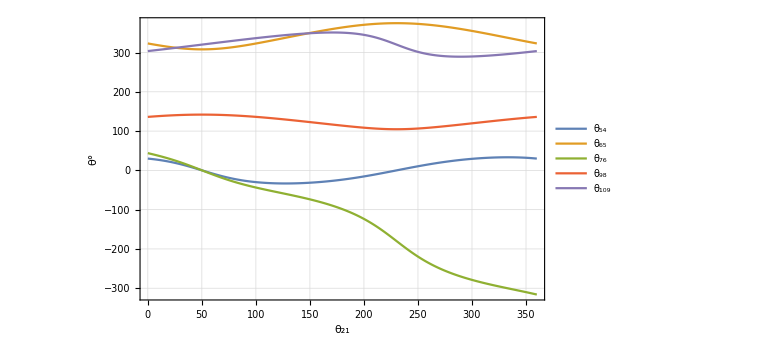

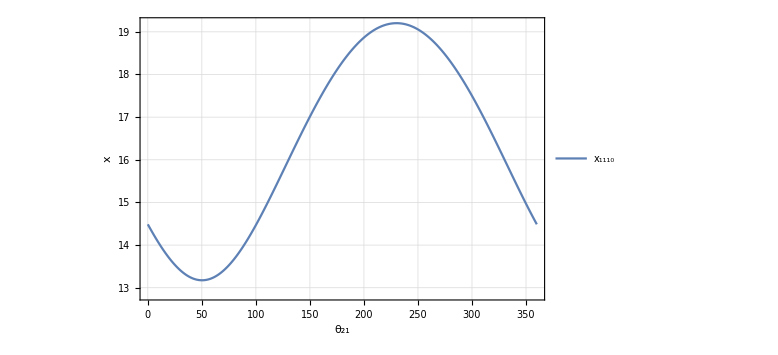

```mathematica
PTable1 = Table[{i,θ54/Degree}/.SolPos[i][[2]],{i,0,360,1}];(*Tabla 1 posición*)
PTable2 = Table[{i,θ65/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable3 = Table[{i,θ76/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable4 = Table[{i,θ98/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable5 = Table[{i,θ109/Degree}/.SolPos[i][[2]],{i,0,360,1}];
PTable6 = Table[{i,x1110/Degree}/.SolPos[i][[2]],{i,0,360,1}];
TablaAngulos = {PTable1, PTable2, PTable3, PTable4, PTable5};
ListLinePlot[TablaAngulos,PlotLegends->{"θ_54", "θ_65", "θ_76", "θ_98", "θ_109"},
Frame->True,FrameLabel->{"θ_21", "θ°"},GridLines->Automatic, ImageSize->Large
]
ListLinePlot[PTable6,PlotLegends->{"x_1110"},
Frame->True,FrameLabel->{"θ_21", "x"},GridLines->Automatic, ImageSize->Large
]
```

## Solución de la Velocidad

```mathematica
Vel1/.PosInicial[[2]]//MatrixForm//Chop
Vel2/.PosInicial[[2]]//MatrixForm//Chop
```

(0.12 dθ21+0.24 dθ65
-0.1 dθ21-0.207846 dθ54-0.09 dθ65
-1. dx1110-0.12 dθ54+0.155885 dθ65)

(dθ54-0.6 dθ76-0.5547 dθ98
0.866025 dθ65-0.4 dθ76+0.83205 dθ98
-1. dθ109+dθ21+0.5 dθ65+0.69282 dθ76)

### Solución inicial

```mathematica
Clear[θ21, θ54, θ65, θ76, θ98,θ109,x1110];
Clear[dθ21, dθ54, dθ65, dθ76, dθ98,dθ109,dx1110];
Clear[ddθ21, ddθ54, ddθ65, ddθ76, ddθ98,ddθ109,ddx1110];
θ21=0*Degree;
dθ21=2π/1;(*1 vuelta en 1 segundo*)
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
VelInicial=Solve[{
Vel1[[1]]==0,
Vel1[[2]]==0,
Vel1[[3]]==0,

Vel2[[1]]==0,
Vel2[[2]]==0,
Vel2[[3]]==0}/.PosInicial[[2]],
{dθ54, dθ65, dθ76, dθ98,dθ109,dx1110}]//Flatten
```

{dθ54→-1.66265,dθ65→-3.14159,dθ76→-4.01129,dθ98→1.34149,dθ109→1.93329,dx1110→-0.290208}

### Solución Total

```mathematica
Clear[θ21, θ54, θ65, θ76, θ98,θ109,x1110];
Clear[dθ21, dθ54, dθ65, dθ76, dθ98,dθ109,dx1110];
Clear[ddθ21, ddθ54, ddθ65, ddθ76, ddθ98,ddθ109,ddx1110];

dθ21=2π/1;(*1 vuelta en 1 segundo*)

For[i=0, i<=360, i+=1,
θ21=i*Degree;
(*θ21=90*Degree;*)
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
SolVel[i]=Solve[{
Vel1[[1]]==0,
Vel1[[2]]==0,
Vel1[[3]]==0,

Vel2[[1]]==0,
Vel2[[2]]==0,
Vel2[[3]]==0}/.SolPos[i][[2]],
{dθ54, dθ65, dθ76, dθ98,dθ109,dx1110}]//Flatten;

];(*Cierra el FOR*)
SolVel[0]
```

{dθ54→-1.66265,dθ65→-3.14159,dθ76→-4.01129,dθ98→1.34149,dθ109→1.93329,dx1110→-0.290208}

## Gráficas de la Velocidad.

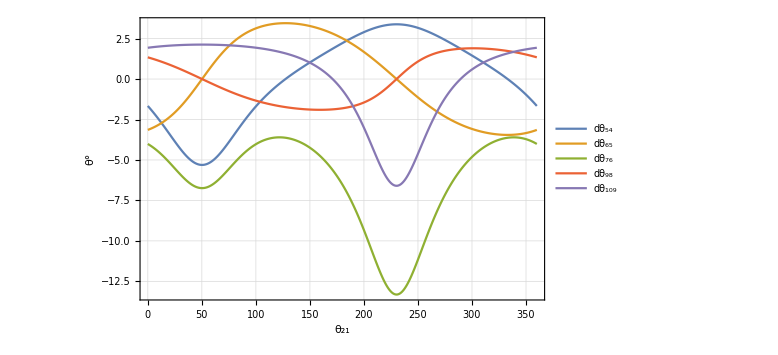

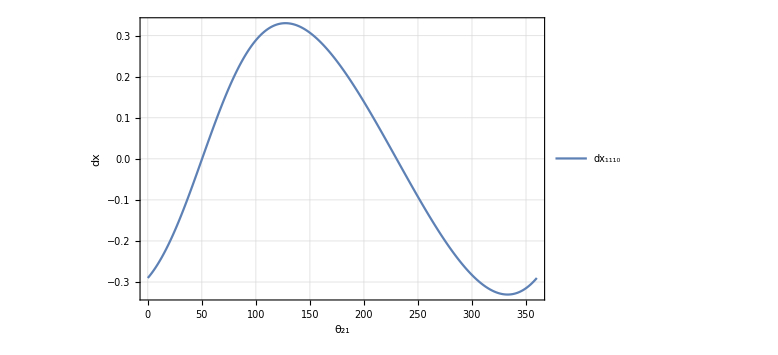

```mathematica
VTable1 = Table[{i,dθ54}/.SolVel[i],{i,0,360,1}];(*Tabla 1 posición*)
VTable2 = Table[{i,dθ65}/.SolVel[i],{i,0,360,1}];
VTable3 = Table[{i,dθ76}/.SolVel[i],{i,0,360,1}];
VTable4 = Table[{i,dθ98}/.SolVel[i],{i,0,360,1}];
VTable5 = Table[{i,dθ109}/.SolVel[i],{i,0,360,1}];
VTable6 = Table[{i,dx1110}/.SolVel[i],{i,0,360,1}];
VTablaAngulos = {VTable1, VTable2, VTable3, VTable4, VTable5};
ListLinePlot[VTablaAngulos,PlotLegends->{"dθ_54", "dθ_65", "dθ_76", "dθ_98", "dθ_109"},
Frame->True,FrameLabel->{"θ_21", "θ°"},GridLines->Automatic, ImageSize->Large
]
ListLinePlot[VTable6,PlotLegends->{"dx_1110"},
Frame->True,FrameLabel->{"θ_21", "dx"},GridLines->Automatic, ImageSize->Large
]
```

## Solución de la Aceleración.

```mathematica
Acel1/.PosInicial[[2]]/.VelInicial//MatrixForm//Chop
Acel2/.PosInicial[[2]]/.VelInicial//MatrixForm//Chop
```

(-2.17131+0.12 ddθ21+0.24 ddθ65
-4.84981-0.1 ddθ21-0.207846 ddθ54-0.09 ddθ65
-3.56614-1. ddx1110-0.12 ddθ54+0.155885 ddθ65)

(14.9368+ddθ54-0.6 ddθ76-0.5547 ddθ98
-7.77605+0.866025 ddθ65-0.4 ddθ76+0.83205 ddθ98
8.40393-1. ddθ109+ddθ21+0.5 ddθ65+0.69282 ddθ76)

### Solución inicial

```mathematica
Clear[θ21, θ54, θ65, θ76, θ98,θ109,x1110];
Clear[dθ21, dθ54, dθ65, dθ76, dθ98,dθ109,dx1110];
Clear[ddθ21, ddθ54, ddθ65, ddθ76, ddθ98,ddθ109,ddx1110];
θ21=0*Degree;
dθ21=2π/1;(*1 vuelta en 1 segundo*)
ddθ21=0;
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
AcelInicial=Solve[{
Acel1[[1]]==0,
Acel1[[2]]==0,
Acel1[[3]]==0,

Acel2[[1]]==0,
Acel2[[2]]==0,
Acel2[[3]]==0}/.PosInicial[[2]]/.VelInicial,
{ddθ54, ddθ65, ddθ76, ddθ98,ddθ109,ddx1110}]//Flatten
```

{ddθ54→-27.2512,ddθ65→9.04714,ddθ76→-14.1636,ddθ98→-6.87992,ddθ109→3.11467,ddx1110→1.11432}

### Solución Total

```mathematica
Clear[θ21, θ54, θ65, θ76, θ98,θ109,x1110];
Clear[dθ21, dθ54, dθ65, dθ76, dθ98,dθ109,dx1110];
Clear[ddθ21, ddθ54, ddθ65, ddθ76, ddθ98,ddθ109,ddx1110];

dθ21=2π/1;(*1 vuelta en 1 segundo*)
ddθ21=0;

For[i=0, i<=360, i+=1,
θ21=i*Degree;
(*θ21=90*Degree;*)
(*Para usar la funcion FindMinimum se deben tener valores aproximados para *)
SolAcel[i]=Solve[{
Acel1[[1]]==0,
Acel1[[2]]==0,
Acel1[[3]]==0,

Acel2[[1]]==0,
Acel2[[2]]==0,
Acel2[[3]]==0}/.SolPos[i][[2]]/.SolVel[i],
{ddθ54, ddθ65, ddθ76, ddθ98,ddθ109,ddx1110}]//Flatten;

];(*Cierra el FOR*)
SolAcel[0]
```

{ddθ54→-27.2512,ddθ65→9.04714,ddθ76→-14.1636,ddθ98→-6.87992,ddθ109→3.11467,ddx1110→1.11432}

## Gráficas de la Aceleración.

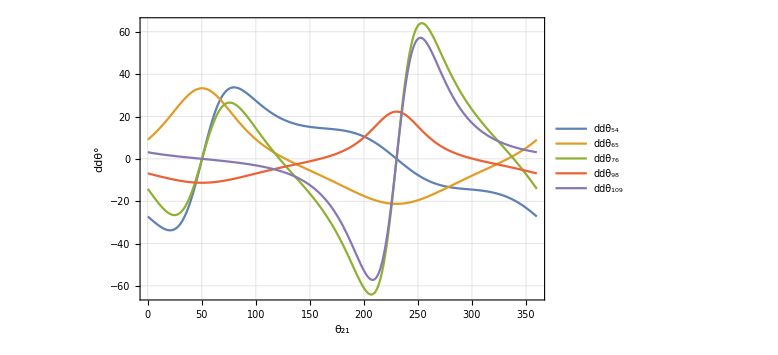

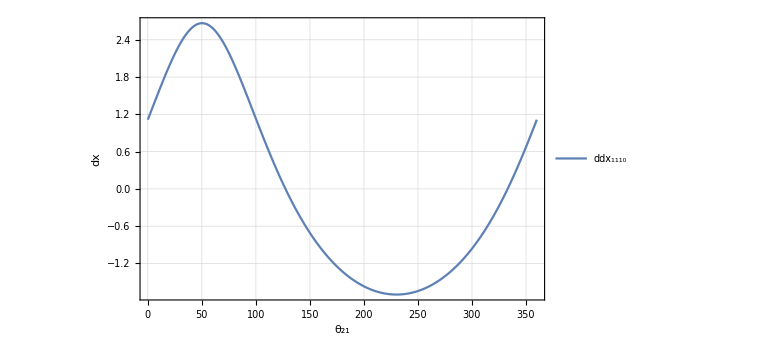

```mathematica
ATable1 = Table[{i,ddθ54}/.SolAcel[i],{i,0,360,1}];(*Tabla 1 posición*)
ATable2 = Table[{i,ddθ65}/.SolAcel[i],{i,0,360,1}];
ATable3 = Table[{i,ddθ76}/.SolAcel[i],{i,0,360,1}];
ATable4 = Table[{i,ddθ98}/.SolAcel[i],{i,0,360,1}];
ATable5 = Table[{i,ddθ109}/.SolAcel[i],{i,0,360,1}];
ATable6 = Table[{i,ddx1110}/.SolAcel[i],{i,0,360,1}];
ATablaAngulos = {ATable1, ATable2, ATable3, ATable4, ATable5};
ListLinePlot[ATablaAngulos,PlotLegends->{"ddθ_54", "ddθ_65", "ddθ_76", "ddθ_98", "ddθ_109"},
Frame->True,FrameLabel->{"θ_21", "ddθ°"},GridLines->Automatic, ImageSize->Large
]
ListLinePlot[ATable6,PlotLegends->{"ddx_1110"},
Frame->True,FrameLabel->{"θ_21", "dx"},GridLines->Automatic, ImageSize->Large
]
```

## Animación con ANIMATE.

```mathematica
Animate[
θ21=i*Degree;

P0 = {0,0,0};
P1=P10;
P2=P10+P32;
P3=P10+P32+P43;
P4=P10+P32+P43+P87;

Tubo1 = Tube[{P0,P1,P2,P3},0.003]/.SolPos[i][[2]];
Esfera1 = Sphere[P3,0.007]/.SolPos[i][[2]];(*Junta esférica*)
Cilindro1 = Cylinder[{P3,P4},0.003]/.SolPos[i][[2]];
Esfera2 = Sphere[P4,0.007]/.SolPos[i][[2]];(*Junta universal simplificada*)
(*_________________________________________Corredera__________________________________________*)

(*Cuboid [Esquina, Contraesquina]]*)
Pmin1 = P4+{0.018,0.007,0.01};
Pmax1 = P4+{-0.018,-0.019,0.04};
Cubo1 = Cuboid [Pmin1, Pmax1]/.SolPos[i][[2]];

Pmin2 = P4+{0.018,0.007,-0.01};
Pmax2 = P4+{-0.018,-0.019,-0.04};
Cubo2 = Cuboid [Pmin2, Pmax2]/.SolPos[i][[2]];
(*Base*)
Pmin3 = {-0.12,-0.143,0.4};
Pmax3 = {0.05,-0.15,-0.02};
Cubo3 = Cuboid [Pmin3, Pmax3]/.SolPos[i][[2]];
(*Chumacera /Base de manivela*)
P5 = {0,0,0.005};
P6 = {0,0,0.015};
Cilindro2 = Cylinder[{P5,P6},0.01];

Cuerpo1 = Graphics3D[{RGBColor[1,1,0],Cubo3,Cilindro2}];
Cuerpo2 = Graphics3D[{RGBColor[1,0,0],Tubo1,Esfera1}];
Cuerpo3 = Graphics3D[{RGBColor[0,1,0],Cilindro1,Esfera2}];
Cuerpo4 = Graphics3D[{RGBColor[0,0,1],Cubo1,Cubo2}];


Show[Cuerpo1,Cuerpo2,Cuerpo3,Cuerpo4,
Axes->True,
AxesLabel->{"X","Y","Z"},
ImageSize->500,
ViewPoint->{2.7872,1.2068,1.4899},
ViewVertical->{0,1,0},
PlotRange->{{-0.15,0.1},{-0.15,0.1},{-0.05,0.4}}
],{i,0,360,1},AnimationRunning-> False,ControlPlacement->Top]
```

-Graphics3D-

## Animación con FOR par GIF.

```mathematica
For[i=0,i<=360,i+=1,
θ21=i*Degree;

P0 = {0,0,0};
P1=P10;
P2=P10+P32;
P3=P10+P32+P43;
P4=P10+P32+P43+P87;

Tubo1 = Tube[{P0,P1,P2,P3},0.003]/.SolPos[i][[2]];
Esfera1 = Sphere[P3,0.007]/.SolPos[i][[2]];(*Junta esférica*)
Cilindro1 = Cylinder[{P3,P4},0.003]/.SolPos[i][[2]];
Esfera2 = Sphere[P4,0.007]/.SolPos[i][[2]];(*Junta universal simplificada*)
(*_________________________________________Corredera__________________________________________*)

(*Cuboid [Esquina, Contraesquina]]*)
Pmin1 = P4+{0.018,0.007,0.01};
Pmax1 = P4+{-0.018,-0.019,0.04};
Cubo1 = Cuboid [Pmin1, Pmax1]/.SolPos[i][[2]];

Pmin2 = P4+{0.018,0.007,-0.01};
Pmax2 = P4+{-0.018,-0.019,-0.04};
Cubo2 = Cuboid [Pmin2, Pmax2]/.SolPos[i][[2]];
(*Base*)
Pmin3 = {-0.12,-0.143,0.4};
Pmax3 = {0.05,-0.15,-0.02};
Cubo3 = Cuboid [Pmin3, Pmax3]/.SolPos[i][[2]];
(*Chumacera /Base de manivela*)
P5 = {0,0,0.005};
P6 = {0,0,0.015};
Cilindro2 = Cylinder[{P5,P6},0.01];

Cuerpo1 = Graphics3D[{RGBColor[1,1,0],Cubo3,Cilindro2}];
Cuerpo2 = Graphics3D[{RGBColor[1,0,0],Tubo1,Esfera1}];
Cuerpo3 = Graphics3D[{RGBColor[0,1,0],Cilindro1,Esfera2}];
Cuerpo4 = Graphics3D[{RGBColor[0,0,1],Cubo1,Cubo2}];


Animacion[i]=Show[Cuerpo1,Cuerpo2,Cuerpo3,Cuerpo4,
Axes->True,
AxesLabel->{"X","Y","Z"},
ImageSize->500,
ViewPoint->{2.7872,1.2068,1.4899},
ViewVertical->{0,1,0},
PlotRange->{{-0.15,0.1},{-0.15,0.1},{-0.05,0.4}}
]];
Mecanismos
```

Mecanismos

TablaFiguras = Table[Animacion[i], {i, 0, 360, 10}];
Export["/home/yeshua/Documentos/sem_10/DinamicaMaquinaria/animacion_gif/mecanismo.gif", TablaFiguras]

/home/yeshua/Documentos/sem_10/DinamicaMaquinaria/animacion_gif/mecanismo.gif